```mathematica
func[t_,tp_,c_,Nmax_]:=Module[{n,f},
f=0;
For[n=1,n≤Nmax,n++,
f+=c[[n]]Sin[n Pi t/tp];
];
f
];
```

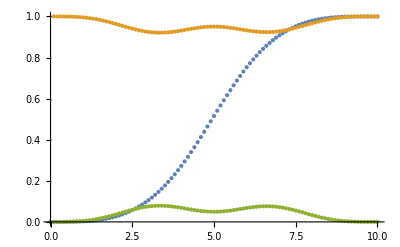

```mathematica
ListPlot[cdat]
```

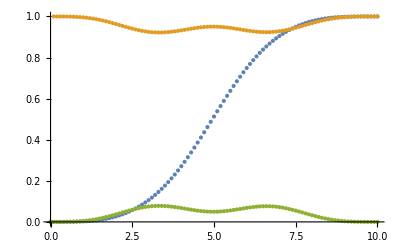

```mathematica
ListPlot[F210]
```

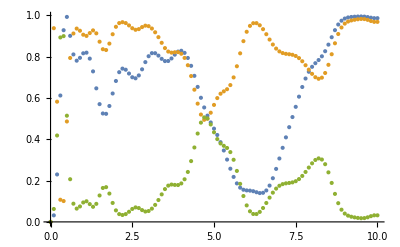

```mathematica
ListPlot[F510]
```

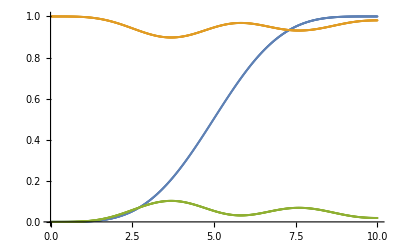

```mathematica
ListPlot[F310min]
```

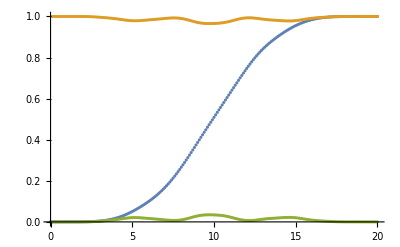

```mathematica
ListPlot[F220]
```

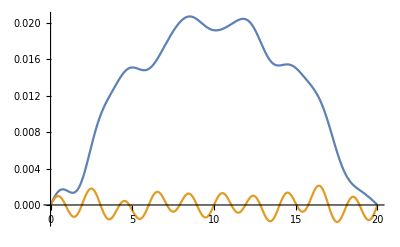

```mathematica
Plot[{func[t,20,P220[[1]],20],func[t,20,P220[[2]],20]},{t,0,20}]
```

```mathematica
P220={{0.0200494,4.03523*10^-05,-0.000354767,1.01328*10^-05,-0.000664413,2.54512*10^-05,-0.0010761,-0.000144541,-0.000993192,-1.40071*10^-05,0.000656784,8.40425*10^-06,2.15173*10^-05,0.00011009,0.000214219,3.09944*10^-06,0.000324488,0.000138164,0.000117004,0.000171006},{7.86781*10^-06,-7.40886*10^-05,-5.45979*10^-05,-7.19428*10^-05,1.00732*10^-05,0.000286579,-7.75456*10^-05,0.000314772,-0.000200331,-0.000244141,-2.58088*10^-05,-0.00012368,-6.00219*10^-05,-0.00010401,2.69413*10^-05,-2.68817*10^-05,-9.77516*10^-06,0.000133336,-0.00010711,0.00128168}};
```

```mathematica
F220={{{0,0},{0.1,9.63957*10^-08},{0.2,8.23511*10^-07},{0.3,3.04742*10^-06},{0.4,7.63638*10^-06},{0.5,1.51272*10^-05},{0.6,2.55117*10^-05},{0.7,3.82223*10^-05},{0.8,5.23227*10^-05},{0.9,6.68338*10^-05},{1,8.10783*10^-05},{1.1,9.49261*10^-05},{1.2,0.000108866},{1.3,0.000123903},{1.4,0.000141354},{1.5,0.000162655},{1.6,0.000189309},{1.7,0.000223032},{1.8,0.000266086},{1.9,0.000321731},{2,0.000394631},{2.1,0.000491084},{2.2,0.00061898},{2.3,0.00078748},{2.4,0.00100647},{2.5,0.00128595},{2.6,0.00163551},{2.7,0.00206402},{2.8,0.00257956},{2.9,0.00318958},{3,0.00390126},{3.1,0.00472175},{3.2,0.00565849},{3.3,0.00671921},{3.4,0.00791194},{3.5,0.00924485},{3.6,0.0107261},{3.7,0.0123639},{3.8,0.0141662},{3.9,0.0161411},{4,0.0182963},{4.1,0.0206392},{4.2,0.0231763},{4.3,0.0259128},{4.4,0.0288519},{4.5,0.0319942},{4.6,0.0353374},{4.7,0.0388765},{4.8,0.0426041},{4.9,0.0465107},{5,0.0505862},{5.1,0.0548203},{5.2,0.0592036},{5.3,0.0637286},{5.4,0.0683897},{5.5,0.0731844},{5.6,0.0781131},{5.7,0.0831798},{5.8,0.0883919},{5.9,0.0937601},{6,0.0992984},{6.1,0.105023},{6.2,0.110953},{6.3,0.117107},{6.4,0.123503},{6.5,0.130159},{6.6,0.137091},{6.7,0.144312},{6.8,0.151832},{6.9,0.159659},{7,0.1678},{7.1,0.176259},{7.2,0.185036},{7.3,0.194132},{7.4,0.203547},{7.5,0.213274},{7.6,0.22331},{7.7,0.233644},{7.79999,0.244267},{7.89999,0.255165},{7.99999,0.266322},{8.09999,0.277719},{8.2,0.289335},{8.3,0.301145},{8.4,0.313123},{8.5,0.325242},{8.6,0.337472},{8.7,0.349784},{8.8,0.362151},{8.9,0.374546},{9,0.386948},{9.1,0.399338},{9.2,0.411699},{9.3,0.424022},{9.4,0.436299},{9.5,0.44853},{9.6,0.460714},{9.7,0.472855},{9.8,0.484959},{9.9,0.497032},{10,0.509083},{10.1,0.521119},{10.2,0.533147},{10.3,0.545171},{10.4,0.557198},{10.5,0.569229},{10.6,0.581266},{10.7,0.593308},{10.8,0.605354},{10.9,0.617401},{11,0.629444},{11.1,0.641476},{11.2,0.653487},{11.3,0.665468},{11.4,0.677402},{11.5,0.689272},{11.6,0.701059},{11.7,0.712739},{11.8,0.724285},{11.9,0.735668},{12,0.746858},{12.1,0.757823},{12.2,0.768533},{12.3,0.778958},{12.4,0.789071},{12.5,0.798852},{12.6,0.808283},{12.7,0.817356},{12.8,0.826066},{12.9,0.834417},{13,0.842417},{13.1,0.850083},{13.2,0.857431},{13.3,0.864485},{13.4,0.871269},{13.5,0.87781},{13.6,0.884131},{13.7,0.890257},{13.8,0.896209},{13.9,0.902002},{14,0.907648},{14.1,0.913152},{14.2,0.918516},{14.3,0.923734},{14.4,0.928802},{14.5,0.933708},{14.6,0.938445},{14.7,0.943002},{14.8,0.947372},{14.9,0.951547},{15,0.955523},{15.1,0.959296},{15.2,0.962867},{15.3,0.966235},{15.4,0.969404},{15.5,0.972378},{15.6,0.975162},{15.7,0.977761},{15.8,0.980183},{15.9,0.98243},{16,0.984508},{16.1,0.98642},{16.2,0.988167},{16.3,0.989754},{16.4,0.991183},{16.5,0.992461},{16.6,0.993594},{16.7,0.994591},{16.8,0.995463},{16.9,0.996219},{17,0.996872},{17.1,0.997431},{17.2,0.997905},{17.3,0.998304},{17.4,0.998636},{17.5,0.998908},{17.6,0.999129},{17.7,0.999307},{17.8,0.999448},{17.9,0.99956},{18,0.99965},{18.1,0.999721},{18.2,0.999778},{18.3,0.999823},{18.4,0.999859},{18.5,0.999887},{18.6,0.999908},{18.7,0.999925},{18.8,0.999939},{18.9,0.999952},{19,0.999964},{19.1,0.999975},{19.2,0.999985},{19.3,0.999992},{19.4,0.999997},{19.5,0.999999},{19.6,0.999998},{19.7,0.999995},{19.8,0.999992},{19.9,0.999991},{20,0.999991}},{{0,0},{0.1,1},{0.2,0.999998},{0.3,0.999994},{0.4,0.999985},{0.5,0.999971},{0.6,0.999952},{0.7,0.999931},{0.8,0.99991},{0.9,0.999891},{1,0.999878},{1.1,0.999872},{1.2,0.999871},{1.3,0.999874},{1.4,0.999877},{1.5,0.999879},{1.6,0.999876},{1.7,0.999864},{1.8,0.99984},{1.9,0.999798},{2,0.999732},{2.1,0.999633},{2.2,0.999491},{2.3,0.999297},{2.4,0.999042},{2.5,0.998721},{2.6,0.998334},{2.7,0.997884},{2.8,0.997379},{2.9,0.996829},{3,0.996244},{3.1,0.995634},{3.2,0.995005},{3.3,0.994359},{3.4,0.993694},{3.5,0.993002},{3.6,0.992274},{3.7,0.991499},{3.8,0.990666},{3.9,0.989765},{4,0.988793},{4.1,0.987751},{4.2,0.986649},{4.3,0.985505},{4.4,0.984347},{4.5,0.98321},{4.6,0.982136},{4.7,0.981168},{4.8,0.980346},{4.9,0.979705},{5,0.979269},{5.1,0.979046},{5.2,0.979034},{5.3,0.979216},{5.4,0.979563},{5.5,0.980042},{5.6,0.980616},{5.7,0.98125},{5.8,0.981915},{5.9,0.982588},{6,0.983255},{6.1,0.983912},{6.2,0.98456},{6.3,0.985206},{6.4,0.985859},{6.5,0.986531},{6.6,0.987229},{6.7,0.987956},{6.8,0.988708},{6.9,0.989475},{7,0.990235},{7.1,0.990961},{7.2,0.991619},{7.3,0.992171},{7.4,0.992578},{7.5,0.992801},{7.6,0.992805},{7.7,0.992562},{7.79999,0.992049},{7.89999,0.991253},{7.99999,0.99017},{8.09999,0.988807},{8.2,0.987183},{8.3,0.985331},{8.4,0.983296},{8.5,0.981135},{8.6,0.978916},{8.7,0.976708},{8.8,0.974585},{8.9,0.972611},{9,0.970842},{9.1,0.969317},{9.2,0.968059},{9.3,0.967072},{9.4,0.966344},{9.5,0.965854},{9.6,0.965569},{9.7,0.965457},{9.8,0.965489},{9.9,0.965642},{10,0.965903},{10.1,0.96627},{10.2,0.966753},{10.3,0.967368},{10.4,0.968138},{10.5,0.969086},{10.6,0.970232},{10.7,0.971588},{10.8,0.973153},{10.9,0.974913},{11,0.976836},{11.1,0.97888},{11.2,0.980988},{11.3,0.983098},{11.4,0.985145},{11.5,0.987065},{11.6,0.9888},{11.7,0.9903},{11.8,0.991528},{11.9,0.992457},{12,0.993073},{12.1,0.993375},{12.2,0.993371},{12.3,0.993086},{12.4,0.992552},{12.5,0.991812},{12.6,0.990916},{12.7,0.989917},{12.8,0.98887},{12.9,0.987822},{13,0.986813},{13.1,0.985875},{13.2,0.985022},{13.3,0.984259},{13.4,0.983578},{13.5,0.982967},{13.6,0.982403},{13.7,0.981868},{13.8,0.981344},{13.9,0.98082},{14,0.980294},{14.1,0.979771},{14.2,0.979271},{14.3,0.978819},{14.4,0.97845},{14.5,0.978201},{14.6,0.978109},{14.7,0.978205},{14.8,0.978513},{14.9,0.979039},{15,0.979779},{15.1,0.980711},{15.2,0.981803},{15.3,0.983011},{15.4,0.98429},{15.5,0.985594},{15.6,0.98688},{15.7,0.988117},{15.8,0.989278},{15.9,0.990349},{16,0.991322},{16.1,0.992198},{16.2,0.992982},{16.3,0.993683},{16.4,0.994315},{16.5,0.99489},{16.6,0.995422},{16.7,0.995924},{16.8,0.996404},{16.9,0.996867},{17,0.997314},{17.1,0.997741},{17.2,0.998142},{17.3,0.998509},{17.4,0.998833},{17.5,0.99911},{17.6,0.999336},{17.7,0.999514},{17.8,0.999648},{17.9,0.999745},{18,0.999811},{18.1,0.999853},{18.2,0.999877},{18.3,0.999887},{18.4,0.999887},{18.5,0.999881},{18.6,0.999872},{18.7,0.999865},{18.8,0.999862},{18.9,0.999866},{19,0.999878},{19.1,0.999897},{19.2,0.99992},{19.3,0.999945},{19.4,0.999966},{19.5,0.999982},{19.6,0.999992},{19.7,0.999998},{19.8,0.999999},{19.9,1},{20,1}},{{0,0},{0.1,1.92538*10^-07},{0.2,1.63764*10^-06},{0.3,6.01414*10^-06},{0.4,1.48946*10^-05},{0.5,2.90051*10^-05},{0.6,4.77512*10^-05},{0.7,6.91946*10^-05},{0.8,9.05038*10^-05},{0.9,0.000108725},{1,0.000121611},{1.1,0.000128234},{1.2,0.000129189},{1.3,0.000126392},{1.4,0.000122587},{1.5,0.000120846},{1.6,0.000124288},{1.7,0.000136189},{1.8,0.000160444},{1.9,0.000202192},{2,0.000268294},{2.1,0.000367365},{2.2,0.00050918},{2.3,0.00070348},{2.4,0.000958417},{2.5,0.00127902},{2.6,0.00166612},{2.7,0.00211602},{2.8,0.00262114},{2.9,0.00317137},{3,0.00375605},{3.1,0.00436589},{3.2,0.00499475},{3.3,0.00564066},{3.4,0.00630618},{3.5,0.00699796},{3.6,0.00772571},{3.7,0.00850073},{3.8,0.00933406},{3.9,0.0102345},{4,0.0112066},{4.1,0.0122487},{4.2,0.013351},{4.3,0.0144951},{4.4,0.0156534},{4.5,0.0167901},{4.6,0.0178642},{4.7,0.0188324},{4.8,0.019654},{4.9,0.0202948},{5,0.0207315},{5.1,0.0209538},{5.2,0.0209657},{5.3,0.0207842},{5.4,0.020437},{5.5,0.0199581},{5.6,0.0193843},{5.7,0.0187501},{5.8,0.0180854},{5.9,0.0174123},{6,0.0167446},{6.1,0.0160878},{6.2,0.0154401},{6.3,0.0147944},{6.4,0.0141408},{6.5,0.0134691},{6.6,0.0127713},{6.7,0.0120443},{6.8,0.0112917},{6.9,0.0105253},{7,0.0097651},{7.1,0.0090389},{7.2,0.00838074},{7.3,0.00782864},{7.4,0.00742202},{7.5,0.00719912},{7.6,0.00719463},{7.7,0.00743775},{7.79999,0.00795056},{7.89999,0.00874666},{7.99999,0.00982992},{8.09999,0.0111932},{8.2,0.012817},{8.3,0.0146691},{8.4,0.016704},{8.5,0.0188645},{8.6,0.0210842},{8.7,0.0232916},{8.8,0.0254151},{8.9,0.0273889},{9,0.0291581},{9.1,0.0306829},{9.2,0.0319411},{9.3,0.0329283},{9.4,0.0336556},{9.5,0.0341463},{9.6,0.0344312},{9.7,0.0345429},{9.8,0.034511},{9.9,0.0343582},{10,0.0340971},{10.1,0.0337297},{10.2,0.0332471},{10.3,0.0326321},{10.4,0.0318622},{10.5,0.030914},{10.6,0.0297677},{10.7,0.0284118},{10.8,0.0268468},{10.9,0.0250875},{11,0.0231639},{11.1,0.0211203},{11.2,0.0190119},{11.3,0.0169015},{11.4,0.0148547},{11.5,0.012935},{11.6,0.0112004},{11.7,0.00969989},{11.8,0.00847181},{11.9,0.00754264},{12,0.00692658},{12.1,0.00662543},{12.2,0.00662873},{12.3,0.00691415},{12.4,0.0074483},{12.5,0.00818834},{12.6,0.00908437},{12.7,0.0100828},{12.8,0.0111305},{12.9,0.0121785},{13,0.0131866},{13.1,0.0141254},{13.2,0.0149784},{13.3,0.0157415},{13.4,0.0164215},{13.5,0.0170335},{13.6,0.0175968},{13.7,0.0181317},{13.8,0.0186556},{13.9,0.0191795},{14,0.0197063},{14.1,0.0202286},{14.2,0.0207291},{14.3,0.0211808},{14.4,0.02155},{14.5,0.0217991},{14.6,0.0218911},{14.7,0.0217946},{14.8,0.0214874},{14.9,0.020961},{15,0.0202212},{15.1,0.0192889},{15.2,0.0181974},{15.3,0.0169889},{15.4,0.01571},{15.5,0.0144064},{15.6,0.0131196},{15.7,0.0118831},{15.8,0.0107217},{15.9,0.00965096},{16,0.00867775},{16.1,0.00780207},{16.2,0.00701831},{16.3,0.00631682},{16.4,0.00568529},{16.5,0.00511011},{16.6,0.00457774},{16.7,0.00407621},{16.8,0.00359641},{16.9,0.00313327},{17,0.00268617},{17.1,0.00225871},{17.2,0.00185764},{17.3,0.00149113},{17.4,0.0011669},{17.5,0.000890411},{17.6,0.00066383},{17.7,0.000485713},{17.8,0.000351572},{17.9,0.000254993},{18,0.000188925},{18.1,0.000146762},{18.2,0.000122922},{18.3,0.000112882},{18.4,0.000112808},{18.5,0.000119061},{18.6,0.000127881},{18.7,0.000135448},{18.8,0.000138316},{18.9,0.000134067},{19,0.000121889},{19.1,0.000102826},{19.2,7.95159*10^-05},{19.3,5.54735*10^-05},{19.4,3.41139*10^-05},{19.5,1.78396*10^-05},{19.6,7.49428*10^-06},{19.7,2.36036*10^-06},{19.8,6.81463*10^-07},{19.9,5.01441*10^-07},{20,5.01396*10^-07}}};
```

```mathematica
F510={{{0,0},{0.1,0.0316647},{0.2,0.229637},{0.3,0.611686},{0.4,0.927716},{0.5,0.992086},{0.6,0.900476},{0.7,0.810486},{0.8,0.780316},{0.9,0.79407},{1,0.815989},{1.1,0.819036},{1.2,0.7903},{1.3,0.728464},{1.4,0.646386},{1.5,0.569947},{1.6,0.524744},{1.7,0.523054},{1.8,0.560949},{1.9,0.621499},{2,0.682061},{2.1,0.724613},{2.2,0.741892},{2.3,0.736533},{2.4,0.718099},{2.5,0.700081},{2.6,0.695027},{2.7,0.708918},{2.8,0.738468},{2.9,0.773313},{3,0.801849},{3.1,0.816692},{3.2,0.816458},{3.3,0.804829},{3.4,0.789156},{3.5,0.778279},{3.6,0.778733},{3.7,0.791093},{3.8,0.809346},{3.9,0.824251},{4,0.828285},{4.1,0.818089},{4.2,0.79337},{4.3,0.755337},{4.4,0.706937},{4.5,0.65337},{4.6,0.600777},{4.7,0.553844},{4.8,0.514364},{4.9,0.481262},{5,0.451382},{5.1,0.420693},{5.2,0.385844},{5.3,0.345631},{5.4,0.301605},{5.5,0.257465},{5.6,0.217721},{5.7,0.186387},{5.8,0.165818},{5.9,0.155623},{6,0.152409},{6.1,0.151271},{6.2,0.148484},{6.3,0.143582},{6.4,0.139479},{6.5,0.140872},{6.6,0.152127},{6.7,0.175696},{6.8,0.211384},{6.9,0.256489},{7,0.306845},{7.1,0.358492},{7.2,0.409112},{7.3,0.458428},{7.4,0.507412},{7.5,0.556853},{7.6,0.606123},{7.7,0.652866},{7.79999,0.69386},{7.89999,0.726583},{7.99999,0.7506},{8.09999,0.768093},{8.2,0.783367},{8.3,0.801452},{8.4,0.826113},{8.5,0.857963},{8.6,0.893801},{8.7,0.927986},{8.8,0.955362},{8.9,0.973752},{9,0.984222},{9.1,0.989429},{9.2,0.991862},{9.3,0.993126},{9.4,0.993956},{9.5,0.994297},{9.6,0.993552},{9.7,0.991325},{9.8,0.988267},{9.9,0.986019},{10,0.986019}},{{0,0},{0.1,0.937438},{0.2,0.581839},{0.3,0.107269},{0.4,0.100861},{0.5,0.486028},{0.6,0.793434},{0.7,0.911841},{0.8,0.935645},{0.9,0.925173},{1,0.906052},{1.1,0.900122},{1.2,0.91387},{1.3,0.92691},{1.4,0.91266},{1.5,0.87216},{1.6,0.835805},{1.7,0.831872},{1.8,0.862919},{1.9,0.90826},{2,0.944249},{2.1,0.962231},{2.2,0.966591},{2.3,0.962196},{2.4,0.950957},{2.5,0.937421},{2.6,0.929832},{2.7,0.933024},{2.8,0.942847},{2.9,0.949752},{3,0.947368},{3.1,0.935874},{3.2,0.917757},{3.3,0.894123},{3.4,0.866779},{3.5,0.841241},{3.6,0.824485},{3.7,0.819209},{3.8,0.821038},{3.9,0.821594},{4,0.813817},{4.1,0.793693},{4.2,0.758281},{4.3,0.705788},{4.4,0.639853},{4.5,0.57236},{4.6,0.519557},{4.7,0.494201},{4.8,0.499633},{4.9,0.528429},{5,0.566238},{5.1,0.599208},{5.2,0.620422},{5.3,0.631847},{5.4,0.642175},{5.5,0.662199},{5.6,0.6993},{5.7,0.75328},{5.8,0.815856},{5.9,0.874762},{6,0.920191},{6.1,0.948663},{6.2,0.961675},{6.3,0.961964},{6.4,0.951626},{6.5,0.932768},{6.6,0.908467},{6.7,0.882517},{6.8,0.858468},{6.9,0.83892},{7,0.825195},{7.1,0.817185},{7.2,0.813415},{7.3,0.811494},{7.4,0.80879},{7.5,0.803036},{7.6,0.792745},{7.7,0.777533},{7.79999,0.758292},{7.89999,0.737034},{7.99999,0.716546},{8.09999,0.7003},{8.2,0.692592},{8.3,0.698176},{8.4,0.720704},{8.5,0.760242},{8.6,0.811437},{8.7,0.864473},{8.8,0.909392},{8.9,0.940911},{9,0.959681},{9.1,0.969669},{9.2,0.97493},{9.3,0.978183},{9.4,0.980686},{9.5,0.98224},{9.6,0.981571},{9.7,0.977828},{9.8,0.972278},{9.9,0.968148},{10,0.968148}},{{0,0},{0.1,0.0625623},{0.2,0.418161},{0.3,0.892731},{0.4,0.899139},{0.5,0.513972},{0.6,0.206566},{0.7,0.0881591},{0.8,0.0643546},{0.9,0.0748273},{1,0.0939484},{1.1,0.099878},{1.2,0.0861301},{1.3,0.0730899},{1.4,0.0873398},{1.5,0.12784},{1.6,0.164195},{1.7,0.168128},{1.8,0.137081},{1.9,0.0917395},{2,0.0557506},{2.1,0.0377686},{2.2,0.0334085},{2.3,0.0378038},{2.4,0.0490426},{2.5,0.0625791},{2.6,0.0701682},{2.7,0.0669765},{2.8,0.0571528},{2.9,0.0502485},{3,0.0526316},{3.1,0.0641259},{3.2,0.0822432},{3.3,0.105877},{3.4,0.133221},{3.5,0.158759},{3.6,0.175515},{3.7,0.180791},{3.8,0.178962},{3.9,0.178406},{4,0.186183},{4.1,0.206307},{4.2,0.241719},{4.3,0.294212},{4.4,0.360147},{4.5,0.42764},{4.6,0.480443},{4.7,0.505799},{4.8,0.500367},{4.9,0.471571},{5,0.433762},{5.1,0.400792},{5.2,0.379578},{5.3,0.368153},{5.4,0.357825},{5.5,0.337801},{5.6,0.3007},{5.7,0.24672},{5.8,0.184144},{5.9,0.125238},{6,0.0798087},{6.1,0.0513369},{6.2,0.0383253},{6.3,0.0380356},{6.4,0.0483739},{6.5,0.0672325},{6.6,0.091533},{6.7,0.117483},{6.8,0.141532},{6.9,0.16108},{7,0.174805},{7.1,0.182815},{7.2,0.186585},{7.3,0.188506},{7.4,0.19121},{7.5,0.196964},{7.6,0.207255},{7.7,0.222467},{7.79999,0.241708},{7.89999,0.262966},{7.99999,0.283454},{8.09999,0.2997},{8.2,0.307408},{8.3,0.301824},{8.4,0.279296},{8.5,0.239758},{8.6,0.188563},{8.7,0.135528},{8.8,0.0906078},{8.9,0.0590894},{9,0.0403191},{9.1,0.0303307},{9.2,0.0250699},{9.3,0.0218171},{9.4,0.0193136},{9.5,0.01776},{9.6,0.0184286},{9.7,0.0221722},{9.8,0.0277217},{9.9,0.0318516},{10,0.0318515}}};
```

```mathematica
F210={{{0,0},{0.1,1.20546*10^-06},{0.2,1.05265*10^-05},{0.3,4.0369*10^-05},{0.4,0.00010659},{0.5,0.000226861},{0.6,0.000420074},{0.7,0.000706779},{0.8,0.00111009},{0.9,0.00165643},{1,0.00237575},{1.1,0.00330094},{1.2,0.00446674},{1.3,0.00590828},{1.4,0.00765985},{1.5,0.00975432},{1.6,0.0122235},{1.7,0.0150991},{1.8,0.0184145},{1.9,0.0222054},{2,0.0265103},{2.1,0.0313697},{2.2,0.0368243},{2.3,0.042913},{2.4,0.0496716},{2.5,0.0571322},{2.6,0.0653239},{2.7,0.0742748},{2.8,0.0840142},{2.9,0.0945732},{3,0.105985},{3.1,0.118282},{3.2,0.131493},{3.3,0.145642},{3.4,0.160743},{3.5,0.176801},{3.6,0.193812},{3.7,0.211766},{3.8,0.230649},{3.9,0.250443},{4,0.271125},{4.1,0.292661},{4.2,0.315008},{4.3,0.338105},{4.4,0.361876},{4.5,0.386227},{4.6,0.411055},{4.7,0.436249},{4.8,0.461698},{4.9,0.487289},{5,0.512916},{5.1,0.538472},{5.2,0.563854},{5.3,0.588957},{5.4,0.613678},{5.5,0.637917},{5.6,0.661582},{5.7,0.684588},{5.8,0.706867},{5.9,0.728362},{6,0.749026},{6.1,0.768824},{6.2,0.787722},{6.3,0.805695},{6.4,0.822719},{6.5,0.838776},{6.6,0.853859},{6.7,0.867974},{6.8,0.881136},{6.9,0.893375},{7,0.904728},{7.1,0.915234},{7.2,0.924933},{7.3,0.933862},{7.4,0.942052},{7.5,0.949531},{7.6,0.956327},{7.7,0.962468},{7.79999,0.967986},{7.89999,0.972917},{7.99999,0.977295},{8.09999,0.981158},{8.2,0.984542},{8.3,0.98748},{8.4,0.990004},{8.5,0.992146},{8.6,0.993937},{8.7,0.995412},{8.8,0.996606},{8.9,0.997554},{9,0.998293},{9.1,0.998854},{9.2,0.99927},{9.3,0.999565},{9.4,0.999765},{9.5,0.999889},{9.6,0.999957},{9.7,0.999988},{9.8,0.999998},{9.9,0.999999},{10,0.999999}},{{0,0},{0.1,0.999998},{0.2,0.999979},{0.3,0.99992},{0.4,0.999789},{0.5,0.999551},{0.6,0.999172},{0.7,0.998613},{0.8,0.997836},{0.9,0.996802},{1,0.995475},{1.1,0.993823},{1.2,0.991821},{1.3,0.989451},{1.4,0.986705},{1.5,0.983584},{1.6,0.980104},{1.7,0.97629},{1.8,0.972184},{1.9,0.96784},{2,0.963322},{2.1,0.958703},{2.2,0.95406},{2.3,0.949468},{2.4,0.945003},{2.5,0.940739},{2.6,0.936752},{2.7,0.933115},{2.8,0.929902},{2.9,0.927179},{3,0.925},{3.1,0.923401},{3.2,0.922399},{3.3,0.921988},{3.4,0.922144},{3.5,0.92283},{3.6,0.924},{3.7,0.925602},{3.8,0.927581},{3.9,0.92987},{4,0.932396},{4.1,0.935071},{4.2,0.937797},{4.3,0.940469},{4.4,0.942983},{4.5,0.945242},{4.6,0.947166},{4.7,0.948689},{4.8,0.949768},{4.9,0.950375},{5,0.950499},{5.1,0.950138},{5.2,0.949306},{5.3,0.948027},{5.4,0.946343},{5.5,0.944308},{5.6,0.941997},{5.7,0.939497},{5.8,0.936903},{5.9,0.934316},{6,0.931832},{6.1,0.92954},{6.2,0.927522},{6.3,0.925848},{6.4,0.924582},{6.5,0.923781},{6.6,0.923495},{6.7,0.923764},{6.8,0.924615},{6.9,0.926054},{7,0.928071},{7.1,0.930631},{7.2,0.933686},{7.3,0.937173},{7.4,0.941022},{7.5,0.945162},{7.6,0.949518},{7.7,0.954016},{7.79999,0.958579},{7.89999,0.963131},{7.99999,0.967597},{8.09999,0.971902},{8.2,0.975983},{8.3,0.979785},{8.4,0.983266},{8.5,0.986398},{8.6,0.989164},{8.7,0.991561},{8.8,0.993595},{8.9,0.995282},{9,0.996645},{9.1,0.997714},{9.2,0.998523},{9.3,0.99911},{9.4,0.999511},{9.5,0.999764},{9.6,0.999906},{9.7,0.999973},{9.8,0.999995},{9.9,1},{10,1}},{{0,0},{0.1,2.40774*10^-06},{0.2,2.09749*10^-05},{0.3,8.02274*10^-05},{0.4,0.000211287},{0.5,0.000448528},{0.6,0.000828007},{0.7,0.00138714},{0.8,0.0021644},{0.9,0.00319822},{1,0.00452495},{1.1,0.00617656},{1.2,0.00817862},{1.3,0.0105487},{1.4,0.0132951},{1.5,0.0164157},{1.6,0.0198964},{1.7,0.0237102},{1.8,0.0278162},{1.9,0.0321604},{2,0.036678},{2.1,0.0412965},{2.2,0.0459401},{2.3,0.0505323},{2.4,0.0549974},{2.5,0.0592609},{2.6,0.0632482},{2.7,0.0668846},{2.8,0.0700977},{2.9,0.072821},{3,0.0750003},{3.1,0.0765988},{3.2,0.0776008},{3.3,0.0780119},{3.4,0.0778559},{3.5,0.07717},{3.6,0.0760001},{3.7,0.0743975},{3.8,0.0724192},{3.9,0.0701296},{4,0.0676038},{4.1,0.0649289},{4.2,0.0622032},{4.3,0.0595312},{4.4,0.0570172},{4.5,0.0547576},{4.6,0.0528343},{4.7,0.0513109},{4.8,0.0502319},{4.9,0.0496246},{5,0.0495014},{5.1,0.0498619},{5.2,0.050694},{5.3,0.0519725},{5.4,0.0536573},{5.5,0.0556918},{5.6,0.0580029},{5.7,0.0605034},{5.8,0.0630971},{5.9,0.0656842},{6,0.0681682},{6.1,0.0704596},{6.2,0.072478},{6.3,0.0741521},{6.4,0.0754182},{6.5,0.0762192},{6.6,0.0765051},{6.7,0.0762358},{6.8,0.0753853},{6.9,0.0739456},{7,0.0719292},{7.1,0.0693688},{7.2,0.0663141},{7.3,0.0628273},{7.4,0.0589777},{7.5,0.0548378},{7.6,0.0504817},{7.7,0.045984},{7.79999,0.0414207},{7.89999,0.0368685},{7.99999,0.0324035},{8.09999,0.0280979},{8.2,0.0240168},{8.3,0.0202147},{8.4,0.0167336},{8.5,0.013602},{8.6,0.0108358},{8.7,0.00843883},{8.8,0.0064047},{8.9,0.00471784},{9,0.00335484},{9.1,0.00228591},{9.2,0.00147672},{9.3,0.000890373},{9.4,0.000489206},{9.5,0.000235842},{9.6,9.36248*10^-05},{9.7,2.72345*10^-05},{9.8,4.58236*10^-06},{9.9,3.72879*10^-07},{10,3.72911*10^-07}}};
```

```mathematica
cdat={{{0,0},{0.1,1.19441*10^-06},{0.2,1.04629*10^-05},{0.3,4.02919*10^-05},{0.4,0.000106872},{0.5,0.00022845},{0.6,0.000424563},{0.7,0.000716218},{0.8,0.00112666},{0.9,0.0016821},{1,0.00241207},{1.1,0.00334891},{1.2,0.00452682},{1.3,0.00598041},{1.4,0.00774351},{1.5,0.00984856},{1.6,0.0123269},{1.7,0.0152099},{1.8,0.0185304},{1.9,0.0223237},{2,0.026628},{2.1,0.0314838},{2.2,0.0369321},{2.3,0.0430127},{2.4,0.0497627},{2.5,0.0572163},{2.6,0.0654051},{2.7,0.0743601},{2.8,0.0841131},{2.9,0.094698},{3,0.10615},{3.1,0.118503},{3.2,0.131788},{3.3,0.146029},{3.4,0.161241},{3.5,0.177426},{3.6,0.194581},{3.7,0.212691},{3.8,0.231739},{3.9,0.251701},{4,0.272548},{4.1,0.294243},{4.2,0.316737},{4.3,0.339969},{4.4,0.363862},{4.5,0.388323},{4.6,0.413254},{4.7,0.438547},{4.8,0.464094},{4.9,0.489787},{5,0.515523},{5.1,0.541196},{5.2,0.566703},{5.3,0.591936},{5.4,0.616788},{5.5,0.641155},{5.6,0.664936},{5.7,0.688044},{5.8,0.710402},{5.9,0.73195},{6,0.752641},{6.1,0.772441},{6.2,0.791321},{6.3,0.809261},{6.4,0.826244},{6.5,0.842258},{6.6,0.857299},{6.7,0.871372},{6.8,0.884492},{6.9,0.896684},{7,0.907979},{7.1,0.918412},{7.2,0.928018},{7.3,0.93683},{7.4,0.944882},{7.5,0.952203},{7.6,0.958825},{7.7,0.964782},{7.79999,0.97011},{7.89999,0.97485},{7.99999,0.97904},{8.09999,0.982723},{8.2,0.985934},{8.3,0.988711},{8.4,0.991085},{8.5,0.993088},{8.6,0.994752},{8.7,0.996109},{8.8,0.997194},{8.9,0.998041},{9,0.998686},{9.1,0.999161},{9.2,0.999497},{9.3,0.999721},{9.4,0.999858},{9.5,0.999928},{9.6,0.999954},{9.7,0.999952},{9.8,0.99994},{9.9,0.999931},{10,0.999931}},{{0,0},{0.1,0.999998},{0.2,0.999979},{0.3,0.99992},{0.4,0.999789},{0.5,0.99955},{0.6,0.999168},{0.7,0.998606},{0.8,0.997826},{0.9,0.996791},{1,0.995467},{1.1,0.993821},{1.2,0.991829},{1.3,0.989472},{1.4,0.986743},{1.5,0.983646},{1.6,0.980193},{1.7,0.976413},{1.8,0.972343},{1.9,0.968033},{2,0.963542},{2.1,0.958937},{2.2,0.954288},{2.3,0.949671},{2.4,0.945159},{2.5,0.94083},{2.6,0.936759},{2.7,0.933024},{2.8,0.929698},{2.9,0.926849},{3,0.924535},{3.1,0.922796},{3.2,0.921656},{3.3,0.92112},{3.4,0.921172},{3.5,0.921783},{3.6,0.922912},{3.7,0.924508},{3.8,0.926509},{3.9,0.928846},{4,0.931436},{4.1,0.934189},{4.2,0.937003},{4.3,0.939773},{4.4,0.942396},{4.5,0.944776},{4.6,0.94683},{4.7,0.948492},{4.8,0.949711},{4.9,0.950455},{5,0.950704},{5.1,0.950453},{5.2,0.949711},{5.3,0.948501},{5.4,0.946864},{5.5,0.944858},{5.6,0.942558},{5.7,0.940054},{5.8,0.937443},{5.9,0.934829},{6,0.932309},{6.1,0.929975},{6.2,0.927911},{6.3,0.926191},{6.4,0.92488},{6.5,0.924035},{6.6,0.923706},{6.7,0.92393},{6.8,0.924732},{6.9,0.926115},{7,0.928068},{7.1,0.930556},{7.2,0.933532},{7.3,0.936937},{7.4,0.940702},{7.5,0.944757},{7.6,0.949031},{7.7,0.95345},{7.79999,0.957942},{7.89999,0.962432},{7.99999,0.966848},{8.09999,0.97112},{8.2,0.975187},{8.3,0.978994},{8.4,0.982499},{8.5,0.985669},{8.6,0.988486},{8.7,0.990942},{8.8,0.99304},{8.9,0.994794},{9,0.996224},{9.1,0.99736},{9.2,0.998233},{9.3,0.99888},{9.4,0.999336},{9.5,0.999638},{9.6,0.999822},{9.7,0.99992},{9.8,0.999965},{9.9,0.999981},{10,0.999981}},{{0,0},{0.1,2.38567*10^-06},{0.2,2.08423*10^-05},{0.3,7.99961*10^-05},{0.4,0.000211387},{0.5,0.000449938},{0.6,0.000831917},{0.7,0.00139424},{0.8,0.00217422},{0.9,0.00320884},{1,0.00453333},{1.1,0.00617907},{1.2,0.00817149},{1.3,0.010528},{1.4,0.0132566},{1.5,0.0163542},{1.6,0.0198066},{1.7,0.023587},{1.8,0.0276572},{1.9,0.0319673},{2,0.0364582},{2.1,0.0410635},{2.2,0.0457118},{2.3,0.0503294},{2.4,0.0548409},{2.5,0.0591703},{2.6,0.0632408},{2.7,0.066976},{2.8,0.0703019},{2.9,0.0731508},{3,0.0754654},{3.1,0.0772042},{3.2,0.0783438},{3.3,0.0788805},{3.4,0.0788285},{3.5,0.0782171},{3.6,0.077088},{3.7,0.0754924},{3.8,0.0734911},{3.9,0.0711544},{4,0.0685637},{4.1,0.065811},{4.2,0.062997},{4.3,0.0602268},{4.4,0.0576037},{4.5,0.0552237},{4.6,0.0531696},{4.7,0.0515081},{4.8,0.0502887},{4.9,0.0495452},{5,0.0492962},{5.1,0.049547},{5.2,0.050289},{5.3,0.0514987},{5.4,0.0531356},{5.5,0.0551418},{5.6,0.0574418},{5.7,0.0599463},{5.8,0.0625567},{5.9,0.0651714},{6,0.0676914},{6.1,0.0700248},{6.2,0.0720886},{6.3,0.0738089},{6.4,0.0751202},{6.5,0.0759649},{6.6,0.0762939},{6.7,0.0760695},{6.8,0.0752683},{6.9,0.0738847},{7,0.0719324},{7.1,0.0694439},{7.2,0.0664676},{7.3,0.0630634},{7.4,0.0592984},{7.5,0.0552429},{7.6,0.0509691},{7.7,0.0465497},{7.79999,0.0420583},{7.89999,0.0375683},{7.99999,0.0331525},{8.09999,0.0288797},{8.2,0.0248128},{8.3,0.0210057},{8.4,0.0175014},{8.5,0.0143311},{8.6,0.0115142},{8.7,0.00905821},{8.8,0.00695996},{8.9,0.00520636},{9,0.00377591},{9.1,0.00264038},{9.2,0.00176693},{9.3,0.00112017},{9.4,0.000663831},{9.5,0.000361752},{9.6,0.000178389},{9.7,7.96136*10^-05},{9.8,3.46201*10^-05},{9.9,1.9149*10^-05},{10,1.91492*10^-05}}};
```